```mathematica
nMax=100;
sqr[x_]:=Quotient[Mod[x^2,10000],10];
t[y_]:=RecurrenceTable[{X[n+1]==sqr[X[n]],X[1]==y},X,{n,1,nMax}];
t[92]
```

{92,846,571,604,481,136,849,80,640,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560,360,960,160,560}

### Графики последовательностей с разными начальным значением

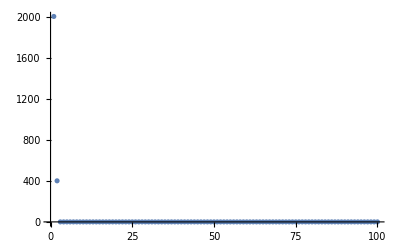
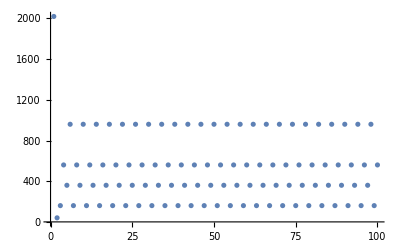
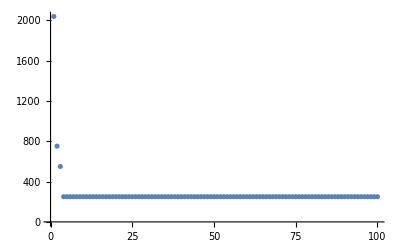
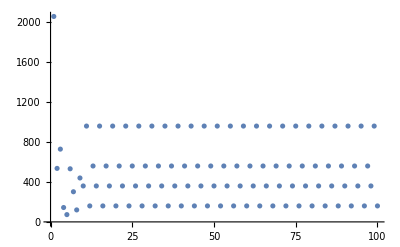
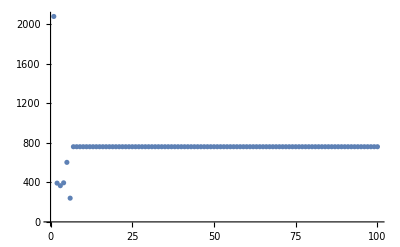
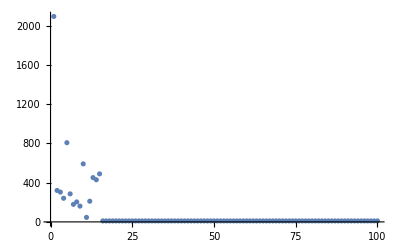
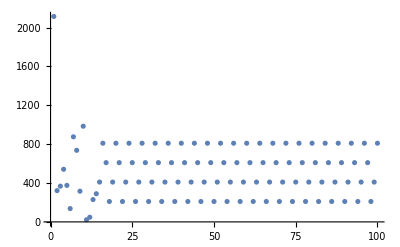
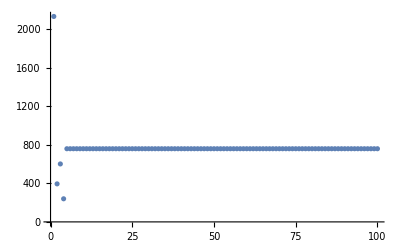

```mathematica
Table[ListPlot[t[s]],{s,2001,4001,19}]
```